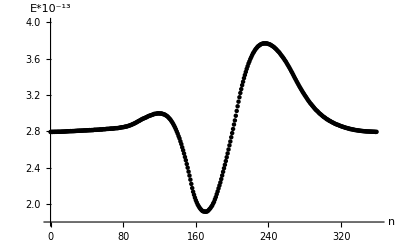

```mathematica
data = Import["/home/artem/projects/solver/build/trace/gloss_curve.txt", "Data"]//Flatten;
n=data[[1]];
(*data = Import["/home/artem/projects/data_claster/trace/gloss_curve.txt", "Data"]//Flatten;*)
curve=Table[{i-2,data[[i]]}, {i,2,n+1}];
pl=ListPlot[curve,PlotStyle->Directive[Black,PointSize[0.008]],
AxesLabel->{"n", "E*10^-13"},
AxesStyle->Directive[Black, 15],
PlotRange->All(*{{0,n},{1.8,4}}*)]
```

```mathematica
an=Animate[Show[pl, Graphics [{Directive[Red,PointSize[0.03]],Point[curve[[i]]]}]], {i,1,n,1}, AnimationRepetitions->1]
```

```mathematica
For[i=1,i<=n,i++,
p=Show[pl, Graphics [{Directive[Red,PointSize[0.03]],Point[curve[[i]]]}]];
Export["/home/artem/projects/data_claster/main_trace/curve_animate"<>ToString[i]<>".png",p]
]
```